```mathematica
X={x,y,z};
Z={xs,ys,zs};
Dist[X_,Z_]:=Sqrt[Total[(X-Z)^2]]
```

```mathematica
Kernel1[X_,Z_,tp_,pl_]:=-1/(-tp)^7(Dist[X,Z]-(pl+tp))^4 (20 Dist[X,Z]^3-35 pl^3+21 pl^2 (pl+tp)-7 pl (pl+tp)^2+(pl+tp)^3+10 Dist[X,Z]^2 (-7 pl+(pl+tp))+4 Dist[X,Z] (21 pl^2-7 pl (pl+tp)+(pl+tp)^2))
```

```mathematica
Q[X_,Z_,tp_,pl_]:=Piecewise[{{1, Dist[X,Z]≤pl}, {0, Dist[X,Z]≥pl+tp}, {Kernel1[X,Z,tp,pl], True}}]
```

```mathematica
D[Kernel1[X,Z,tp,pl],y]//Simplify;
```

```mathematica
G[x_]=a x^5+b x^4+c x^3+d x^2+e x + k;
G[x1]==1; G[x2]==0;G'[x1]==0;G'[x2]==0; G''[x1]==0;G''[x2]==0;
sol=Solve[{G[x1]==1, G[x2]==0,G'[x1]==0,G'[x2]==0, G''[x1]==0,G''[x2]==0},{a,b,c,d,e,k}];
```

```mathematica
G2[x_]=o x^7+l x^6+a x^5+b x^4+c x^3+d x^2+e x + k;
G2[x1]==1; G2[x2]==0;G2'[x1]==0;G2'[x2]==0; G2''[x1]==0;G2''[x2]==0;
sol=Solve[{G2[x1]==1, G2[x2]==0,G2'[x1]==0,G2'[x2]==0, G2''[x1]==0,G2''[x2]==0, G2'''[x1]==0,G2'''[x2]==0},{o,l,a,b,c,d,e,k}];
```

```mathematica
g[x_,x1_,x2_]:=(6 x^5)/(x1-x2)^5+(30 x x1^2 x2^2)/(x1-x2)^5-(15 x^4 (x1+x2))/(x1-x2)^5+(10 x^3 (x1^2+4 x1 x2+x2^2))/(x1-x2)^5-(30 x^2 (x1^2 x2+x1 x2^2))/(x1-x2)^5-(10 x1^2 x2^3-5 x1 x2^4+x2^5)/(x1-x2)^5
```

```mathematica
g2[x_,x1_,x2_]:=-((x-x2)^4 (20 x^3-35 x1^3+21 x1^2 x2-7 x1 x2^2+x2^3+10 x^2 (-7 x1+x2)+4 x (21 x1^2-7 x1 x2+x2^2)))/(x1-x2)^7
```

```mathematica
g3[X_,Z_,pl_,tp_]:=-1/(-tp)^7(Dist[X,Z]-(pl+tp))^4 (20 Dist[X,Z]^3-35 pl^3+21 pl^2 (pl+tp)-7 pl (pl+tp)^2+(pl+tp)^3+10 Dist[X,Z]^2 (-7 pl+(pl+tp))+4 Dist[X,Z] (21 pl^2-7 pl (pl+tp)+(pl+tp)^2))
```

```mathematica
a=D[Kernel1[{x,y,z},{z1,z2,z3},2,1],x]//Simplify;
```

```mathematica
b=D[Kernel1[{x,y,z},{z1,z2,z3},2,1],z1]//Simplify;
```

```mathematica
a+b (* \partial_z^i W = - \partial_i W*)
```

0

```mathematica
Plot3D[Q[{x,y,0},{0,0,0},2,1],{x,-4,4},{y,-4,4}]
```

-Graphics3D-

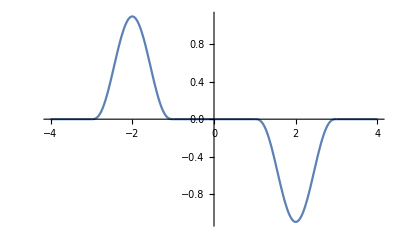

```mathematica
Plot[Evaluate[D[Q[{x,0,0},{0,0,0},2,1],x]],{x,-4,4},PlotRange->All]
```

```mathematica
Plot3D[Evaluate[D[Q[{x,y,0},{0,0,0},2,1],x]],{x,-4,4},{y,-4,4},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[D[Q[{x,y,0},{0,0,0},2,1],{x,2}]],{x,-4,4},{y,-4,4},PlotRange->All]
```

-Graphics3D-

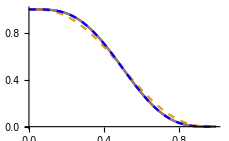

```mathematica
Plot[{Q[{x,0,0},{0,0,0},1,0],g[x,0,1],g2[x,0,1],g3[{x,0,0},{0,0,0},0,1]},{x,0,1},PlotStyle->{Red,Dashed,Gray,{Blue,Dashed}}]
```

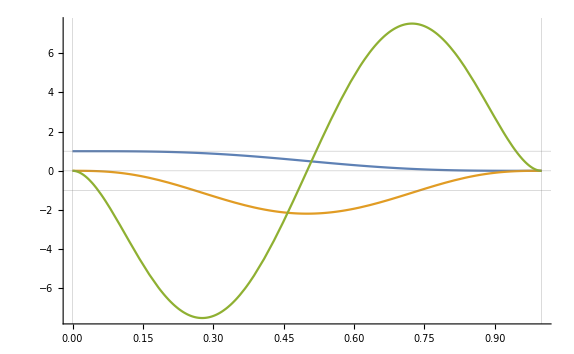

```mathematica
Plot[{g2[x,0,1],Evaluate[D[g2[x,0,1],x]],Evaluate[D[g2[x,0,1],{x,2}]]},{x,0,1},PlotRange->All,GridLines->{{-1,0,1}, {-1,0,1}}]
```

```mathematica
Φ[X_,Z_]:=1/Dist[X,Z];
Ψx[X_,Z_]:=-(X[[1]]-Z[[1]])/Dist[X,Z]^3;
Ψy[X_,Z_]:=-(X[[2]]-Z[[2]])/Dist[X,Z]^3;
Ψz[X_,Z_]:=-(X[[3]]-Z[[3]])/Dist[X,Z]^3;
D[Ψx[X,Z],x]+D[Ψy[X,Z],y]+D[Ψz[X,Z],z]//Simplify
```

0

```mathematica
Ψxr[X_,Z_,tp_,pl_]:=-Φ[X,Z] D[Q[X,Z,tp,pl],x]+Ψx[X,Z]*(1-Q[X,Z,tp,pl]);
Ψyr[X_,Z_,tp_,pl_]:=-Φ[X,Z] D[Q[X,Z,tp,pl],y]+Ψy[X,Z]*(1-Q[X,Z,tp,pl]);
Ψzr[X_,Z_,tp_,pl_]:=-Φ[X,Z] D[Q[X,Z,tp,pl],z]+Ψz[X,Z]*(1-Q[X,Z,tp,pl]);
```

```mathematica
Plot3D[Evaluate[Ψxr[{x,y,0},{0,0,0},1,1]],{x,-4,4},{y,-4,4},PlotPoints->100,PlotRange->All,Exclusions->None]
```

-Graphics3D-

```mathematica
tp=1;pl=1;
SumΨ=D[Ψxr[X,{0,0,0},tp,pl],x]+D[Ψyr[X,{0,0,0},tp,pl],y]+D[Ψzr[X,{0,0,0},tp,pl],z];
rhsTerm1=Φ[X,{0,0,0}](D[Q[X,{0,0,0},tp,pl],{x,2}]+D[Q[X,{0,0,0},tp,pl],{y,2}]+D[Q[X,{0,0,0},tp,pl],{z,2}]);
rhsTerm2=2(D[Q[X,{0,0,0},tp,pl],x]Ψx[X,{0,0,0}]+D[Q[X,{0,0,0},tp,pl],y]Ψy[X,{0,0,0}]+D[Q[X,{0,0,0},tp,pl],z]Ψz[X,{0,0,0}]);
```

```mathematica
SumΨ+rhsTerm1+rhsTerm2//Simplify
```

0